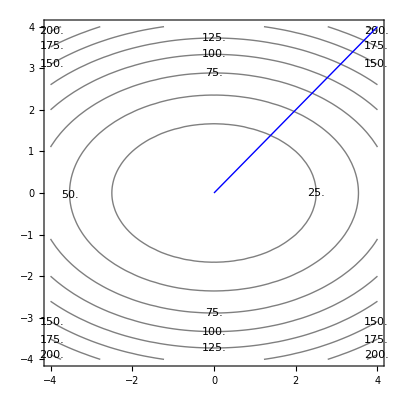

```mathematica
Show[ContourPlot[4 x^2+9 y^2,{x,-4,4},{y,-4,4},ContourShading->False,ContourLabels->True],Plot[x,{x,0,4},PlotStyle->{Thick,Blue}]]
```

```mathematica
ContourPlot3D[{z==4 x^2+9 y^2},{x,-4,4},{y,-4,4},{z,0,225},MeshFunctions->{#3&},ContourStyle->{Opacity[0.4]},BoundaryStyle->{Thick, Red},PlotPoints->60,MeshStyle->{Red}]
```

-Graphics3D-

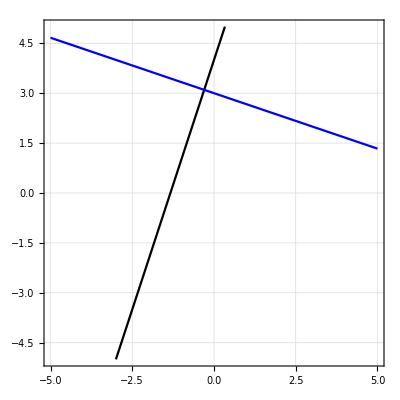

```mathematica
ContourPlot[{y==3x+4,y==-1/3 x+3},{x,-5,5},{y,-5,5},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed],ContourStyle->{{Black},{Blue}}]
```

```mathematica
v[x_,y_]:={x^2+y^2,y-4};
```

```mathematica
w[x_,y_]:={1,-1/(v[x,y][[2]]/v[x,y][[1]])}
```

```mathematica
stream1=StreamPlot[v[x,y],{x,-5,5},{y,-5,5},StreamStyle->{Arrowheads[0],Thin,Black},Background->RGBColor[0.5,0.5,0.5,0.22]];
```

```mathematica
stream2=StreamPlot[w[x,y],{x,-5,5},{y,-5,5},StreamStyle->{Arrowheads[0],Thin,Blue}];
```

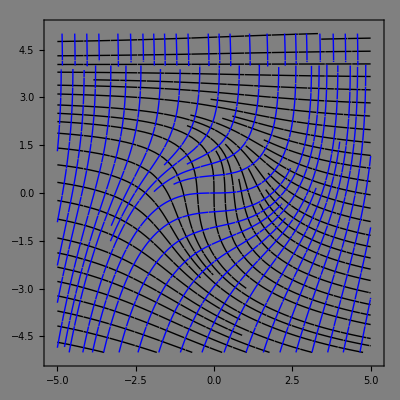

```mathematica
Show[stream1,stream2]
```

```mathematica
vector1=VectorPlot[v[x,y],{x,-5,5},{y,-5,5},VectorStyle->{Black},Background->RGBColor[0.5,0.5,0.5,0.22]];
```

```mathematica
vector2=VectorPlot[w[x,y],{x,-5,5},{y,-5,5},VectorStyle->{Blue}];
```